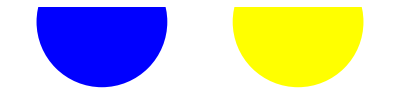

```mathematica
Psat1[T_]=10^(5.074-1657.4/(T+226.9));
v1=0.2;
v2=0.6;
flasks=Show[
Graphics[{Blue,Disk[{0,0}]},PlotRange->{-1,v1}],
Graphics[{Yellow,Disk[{3,0}]},PlotRange->{-1,v2}]
]
```

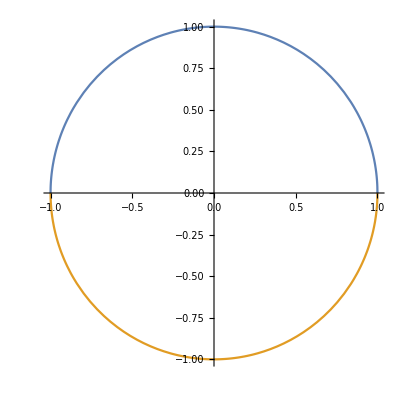

```mathematica
Plot[{√(1-x^2),-(√(1-x^2))},{x,-1,1},AspectRatio->1]
```

```mathematica
Solve[(x-x1)^2+(y)^2==r^2,y]
```

{{y→-√(r^2-x^2+2 x x1-x1^2)},{y→√(r^2-x^2+2 x x1-x1^2)}}

```mathematica
t=ArcSin[0.2]
Cos[π-t]
```

0.201358

-0.979796

```mathematica
Manipulate[
Module[{r,x1,θ1,min},
r=1;x1=3;
θ=ArcSin[v];
min=Cos[-π-θ];
Show[
Plot[{√(r^2-x^2),-√(r^2-x^2),v},{x,Cos[θ],Cos[-π-θ]},(*PlotStyle->{{Thick,Black},{Thick,Black},(*None*){Thick,Black}},Filling->{1->{2}},*)Epilog->Inset[Graphics[{PointSize[Large],Red,Point[{min,v}]}],{min,v}]],
Plot[{√(r^2-x^2-x1^2+2*x*x1),-√(r^2-x^2-x1^2+2*x*x1)},{x,x1-1,x1+1},PlotStyle->{{Thick,Black},{Thick,Black}}],AspectRatio->Automatic,PlotRange->{{-1.25,4.25},{-1.25,1.25}},ImageSize->Large]
],
{{v,0.2,""},0,1,0.1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[{},
θ=ArcSin[V];
Graphics[Disk[{0,0},1,(*{0,2*π},*){θ,π-θ}]]
],
{{V,0.6,""},0,1,0.1,Appearance->"Labeled"}
]
```

```mathematica
p=ArcSin[0.6]
```

0.643501

```mathematica
Manipulate[
Module[{r,θ1,θ2,θ3,θ4,p1,p2,spec1,spec2,spec3},
r=1;
θ1=ArcSin[v1];
θ2=-π-θ1;
θ3=ArcSin[v2];
θ4=-π-θ3;

spec1=Sequence[AspectRatio->Automatic,PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->False];
spec2=Sequence[PlotStyle->{Thick,Black},Filling->Axis];
spec3=Sequence[PlotStyle->{Thick,Black}];
p1=Show[
Plot[-√(r^2-x^2),{x,-1,1},Evaluate@spec2],
Plot[√(r^2-x^2),{x,-1,Cos[θ2]},Evaluate@spec2],
Plot[√(r^2-x^2),{x,Cos[θ1],1},Evaluate@spec2],
Plot[v1,{x,Cos[θ1],Cos[θ2]},Evaluate@spec2],
Plot[{√(r^2-x^2),-√(r^2-x^2)},{x,-1,1},PlotStyle->{{Thick,Black},Black}],Evaluate@spec1
];
p2=Show[
Plot[√(r^2-x^2),{x,-1,1},Evaluate@spec3],
Plot[-√(r^2-x^2),{x,-1,Cos[θ4]},Evaluate@spec3],
Plot[-√(r^2-x^2),{x,Cos[θ3],1},Evaluate@spec3],
Plot[v2,{x,Cos[θ4],Cos[θ3]},Evaluate@spec3],
Plot[-√(r^2-x^2),{x,Cos[θ4],Cos[θ3]},PlotStyle->{Thick,Black},Filling->v2],
Evaluate@spec1
];
Grid[{{Show[p1],Show[p2]}}]
],Grid[{
{Control[{{v1,0.2,"v1"},0.01,1,0.1,Appearance->"Labeled"}],Control[{{v2,-0.2,"v2"},-0.99,-0.01,0.1,Appearance->"Labeled"}]}
}]
]
```